```mathematica
ds=r s(1-s/K)-β[v] s (ia+ic)+γ ia-β[vm] s (iam+icm)+γ iam;
dia=p β[v] s (ia+ic)-v ia-γ ia;
dic=(1-p) β[v] s (ia+ic)-v ic;
diam=p β[vm] s (iam+icm)-vm iam-γ iam;
dicm=(1-p) β[vm] s (iam+icm)-vm icm;
```

```mathematica
J=D[{ds,dia,dic,diam,dicm},{{s,ia,ic,iam,icm}}]/.{iam->0,icm->0};
MatrixForm[J]
```

(-(r s)/K+r (1-s/K)-(ia+ic) β[v] | γ-s β[v] | -s β[v] | γ-s β[vm] | -s β[vm]
(ia+ic) p β[v] | -v-γ+p s β[v] | p s β[v] | 0 | 0
(ia+ic) (1-p) β[v] | (1-p) s β[v] | -v+(1-p) s β[v] | 0 | 0
0 | 0 | 0 | -vm-γ+p s β[vm] | p s β[vm]
0 | 0 | 0 | (1-p) s β[vm] | -vm+(1-p) s β[vm])

```mathematica
(* Use NGM to find the invasion fitness for the bottom right submatrix*)
```

```mathematica
F={{s p β[vm],s p β[vm]},{s (1-p) β[vm],s (1-p) β[vm]}};
V={{vm+γ,0},{0,vm}};
J[[4;;5,4;;5]]==F-V
Eigenvalues[-V] (* must be negative *)
Inverse[V] (* must be non-negative *)
Eigenvalues[F.Inverse[V]]
```

True

{-vm,-vm-γ}

{{vm/(vm^2+vm γ),0},{0,(vm+γ)/(vm^2+vm γ)}}

{0,(s (vm+γ-p γ) β[vm])/(vm (vm+γ))}

```mathematica
(* Mutant can invade if (s (vm+γ-p γ) β[vm])/(vm (vm+γ)) > 1 *)
```

```mathematica
(* Fitness gradient *)
Simplify[D[(s (vm+γ-p γ) β[vm])/(vm (vm+γ)),vm]]
```

(s (-((vm^2-2 (-1+p) vm γ-(-1+p) γ^2) β[vm])+vm (vm+γ) (vm+γ-p γ) β'[vm]))/(vm^2 (vm+γ)^2)

```mathematica
(* ESS virulence solves *)
```

```mathematica
Solve[(-((vm^2-2 (-1+p) vm γ-(-1+p) γ^2) β[vm])+vm (vm+γ) (vm+γ-p γ) β'[vm])==0/.{β[vm]->β0 vm/(h+vm),β'[vm]->D[β0 vm/(h+vm),vm]},vm]//Simplify
```

{{vm→0},{vm→0},{vm→(-1+p) γ-√(p γ (h+(-1+p) γ))},{vm→(-1+p) γ+√(p γ (h+(-1+p) γ))}}

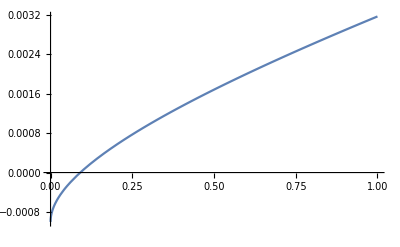

```mathematica
Plot[(-1+p) γ+√(p γ (h+(-1+p) γ))/.{h->0.01,γ->0.001},{p,0,1}]
```

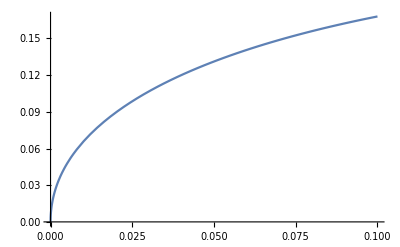

```mathematica
Plot[(-1+p) γ+√(p γ (h+(-1+p) γ))/.{h->1,p->0.5},{γ,0,0.1}]
```

```mathematica
(* How does recovery affect evolution of virulence? *)
Simplify[D[(-1+p) γ+√(p γ (h+(-1+p) γ)),p]]
```

γ+(γ (h+(-1+2 p) γ))/(2 √(p γ (h+(-1+p) γ)))

```mathematica
(* If 2 γ ϵ >= h, then increasing recovery actually decreases virulence *)
(* So if recovery rates are high or the probability of a chronic infection is high, more likely that increasing recovery will decrease virulence *)

(* Assuming 2 γ ϵ < h, then increasing recovery will increase virulence if *)
```

```mathematica
-ϵ+((-1+ϵ) (-h+2 γ ϵ))/(2 √(γ (-1+ϵ) (-h+γ ϵ)))>0;
((-1+ϵ) (-h+2 γ ϵ))/(2 √(γ (-1+ϵ) (-h+γ ϵ)))>ϵ;
(-1+ϵ) (-h+2 γ ϵ)>2 ϵ √(γ (-1+ϵ) (-h+γ ϵ));
((-1+ϵ) (-h+2 γ ϵ))^2>(2 ϵ √(γ (-1+ϵ) (-h+γ ϵ)))^2;
Simplify[Expand[((-1+ϵ) (-h+2 γ ϵ))^2>(2 ϵ √(γ (-1+ϵ) (-h+γ ϵ)))^2]]
```

(-1+ϵ) (-h^2 (-1+ϵ)-4 h γ ϵ+4 γ^2 ϵ^2)<0

```mathematica
(* Notice that the first term is definitely negative *)
(* The second term can be rewritten as *)
-h^2 (-1+ϵ)-4 h γ ϵ+4 γ^2 ϵ^2==Expand[ (-h+2 γ ϵ)^2-ϵ h^2]//Simplify
```

True

```mathematica
(* If (-h+2 γ ϵ)^2-ϵ h^2 > 0 then increasing recovery will increase virulence *)
```

```mathematica
(* How does increasing the probability of chronic infection affect virulence evolution? *)
```

```mathematica
Simplify[D[-γ ϵ+√(h γ-h γ ϵ-γ^2 ϵ+γ^2 ϵ^2),ϵ]]
```

1/2 γ (-2+(-h+γ (-1+2 ϵ))/(√(γ (-1+ϵ) (-h+γ ϵ))))

```mathematica
(* If -h-γ+2 γ ϵ < 0, increasing the probability of chronic infection decreases virulence *)

(* If -h-γ+2 γ ϵ > 0, increasing the probability of chronic infection increases virulence *)
```

```mathematica
-2+(-h+γ (-1+2 ϵ))/(√(γ (-1+ϵ) (-h+γ ϵ)))>0;
(-h+γ (-1+2 ϵ))/(√(γ (-1+ϵ) (-h+γ ϵ)))>2;
-h+γ (-1+2 ϵ)>2 √(γ (-1+ϵ) (-h+γ ϵ));
(-h+γ (-1+2 ϵ))^2>(2 √(γ (-1+ϵ) (-h+γ ϵ)))^2;
Simplify[Expand[(-h+γ (-1+2 ϵ))^2>(2 √(γ (-1+ϵ) (-h+γ ϵ)))^2]]
```

(h-γ)^2>0

```mathematica
ds=r s(1-s/K)-β[v] s (ia+ic)+γ ia-β[vm] s (iam+icm)+γ iam;
dia=p[v] β[v] s (ia+ic)-v ia-γ ia;
dic=(1-p[v]) β[v] s (ia+ic)-v ic;
diam=p[vm] β[vm] s (iam+icm)-vm iam-γ iam;
dicm=(1-p[vm]) β[vm] s (iam+icm)-vm icm;
```

```mathematica
J=D[{ds,dia,dic,diam,dicm},{{s,ia,ic,iam,icm}}]/.{iam->0,icm->0};
MatrixForm[J]
```

(-(r s)/K+r (1-s/K)-(ia+ic) β[v] | γ-s β[v] | -s β[v] | γ-s β[vm] | -s β[vm]
(ia+ic) p[v] β[v] | -v-γ+s p[v] β[v] | s p[v] β[v] | 0 | 0
(ia+ic) (1-p[v]) β[v] | s (1-p[v]) β[v] | -v+s (1-p[v]) β[v] | 0 | 0
0 | 0 | 0 | -vm-γ+s p[vm] β[vm] | s p[vm] β[vm]
0 | 0 | 0 | s (1-p[vm]) β[vm] | -vm+s (1-p[vm]) β[vm])

```mathematica
(* Use NGM to find the invasion fitness for the bottom right submatrix*)
```

```mathematica
F={{s p[vm] β[vm],s p[vm] β[vm]},{s (1-p[vm]) β[vm],s (1-p[vm]) β[vm]}};
V={{vm+γ,0},{0,vm}};
J[[4;;5,4;;5]]==F-V
Eigenvalues[-V] (* must be negative *)
Inverse[V] (* must be non-negative *)
Eigenvalues[F.Inverse[V]]
```

True

{-vm,-vm-γ}

{{vm/(vm^2+vm γ),0},{0,(vm+γ)/(vm^2+vm γ)}}

{0,(s (vm+γ-γ p[vm]) β[vm])/(vm (vm+γ))}

```mathematica
Simplify[D[(s (vm+γ-γ p[vm]) β[vm])/(vm (vm+γ)),vm]]
```

(s (β[vm] (γ (2 vm+γ) p[vm]-(vm+γ) (vm+γ+vm γ p'[vm]))+vm (vm+γ) (vm+γ-γ p[vm]) β'[vm]))/(vm^2 (vm+γ)^2)

```mathematica
InvFit=(β[vm] (γ (2 vm+γ) p[vm]-(vm+γ) (vm+γ+vm γ p'[vm]))+vm (vm+γ) (vm+γ-γ p[vm]) β'[vm])
```

β[vm] (γ (2 vm+γ) p[vm]-(vm+γ) (vm+γ+vm γ p'[vm]))+vm (vm+γ) (vm+γ-γ p[vm]) β'[vm]

```mathematica
Simplify[(InvFit/.{β[vm]->β0 vm/(h+vm),β'[vm]->D[β0 vm/(h+vm),vm],p[vm]->Exp[-ϵ vm],p'[vm]->D[Exp[-ϵ vm],vm]})==0]
```

(ⅇ^(-vm ϵ) vm β0 (ⅇ^(vm ϵ) (vm+γ)^2-γ (h+2 vm+γ+h vm ϵ+vm^2 ϵ+h γ ϵ+vm γ ϵ)))/(h+vm)==0

```mathematica
Solve[(-((vm^2-2 (-1+p) vm γ-(-1+p) γ^2) β[vm])+vm (vm+γ) (vm+γ-p γ) β'[vm])==0/.//Simplify
```

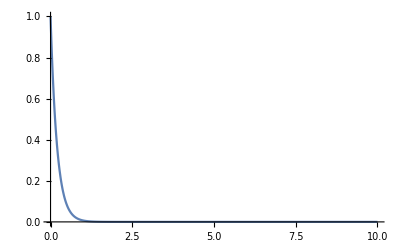

```mathematica
Plot[Exp[-a v]/.{a->5},{v,0,10},PlotRange->All]
```

```mathematica
D[Exp[-ϵ vm],vm]
```

-ⅇ^(-vm ϵ) ϵ

{vm→0.759313}

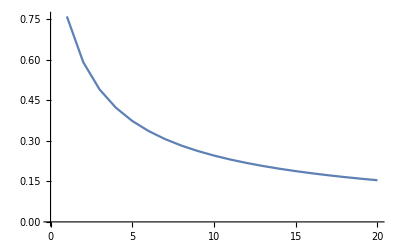

```mathematica
FindRoot[(ⅇ^(vm ϵ) (vm+γ)^2-γ (h+2 vm+γ+h vm ϵ+vm^2 ϵ+h γ ϵ+vm γ ϵ))/.{γ->1,ϵ->1,h->1},{vm,1}]
ListLinePlot[Table[{ee,FindRoot[(ⅇ^(vm ϵ) (vm+γ)^2-γ (h+2 vm+γ+h vm ϵ+vm^2 ϵ+h γ ϵ+vm γ ϵ))/.{γ->1,ϵ->ee,h->1},{vm,1}][[1,2]]},{ee,1,20}]]
```